```mathematica
R[N_]:=(Table[1/(√N)Exp[I*2(k-1)(j-1)/N Pi],{j,1,N},{k,1,N}]);RR:=RandomReal[NormalDistribution[0,1]];
RC:=RR+I*RR;
RG[n_]:=Table[RC,{n},{n}];
RU[n_]:=Orthogonalize[RG[n]];
```

```mathematica
F4[i_]:=(SeedRandom[i];RU[4]).{{0.4,0,0,0},{0,0.3,0,0},{0,0,0.2,0},{0,0,0,0.1}}.ConjugateTranspose[(SeedRandom[i];RU[4])];
T4[i_]:=2Abs[(F4[i])[[1,2]]]+2Abs[(F4[i])[[1,3]]]+2Abs[(F4[i])[[1,4]]]+2Abs[(F4[i])[[2,3]]]+2Abs[(F4[i])[[2,4]]]+2Abs[(F4[i])[[3,4]]];
```

```mathematica
2 √((0.4-0.2)^2+(0.3-0.1)^2)+√((0.4-0.3+0.2-0.1)^2)
```

```mathematica
0.7656854249492381
```

```mathematica
G4[n_]=Table[T4[i],{i,1,n}];
```

Table::iterb: Iterator {i, 1, n} does not have appropriate bounds.

```mathematica
Max[G4[100]]
```

0.717228

```mathematica
Max[G4[1000]]
```

0.756809

```mathematica
Max[G4[10000]]
```

0.760992

```mathematica
Max[G4[100000]]
```

0.768903

```mathematica
Ordering[G4[100000],-1]
```

{49839}

```mathematica
T4[49839]
```

0.768903

```mathematica
SeedRandom[49839];RU[4]//MatrixForm
```

(-0.124529+0.530083 ⅈ | -0.123962-0.101396 ⅈ | -0.198003+0.642453 ⅈ | -0.459698-0.120763 ⅈ
-0.144461+0.387881 ⅈ | 0.479104-0.424096 ⅈ | -0.0668703-0.377343 ⅈ | -0.17681+0.491082 ⅈ
-0.602626+0.0404941 ⅈ | -0.0363396-0.270315 ⅈ | 0.485894+0.303822 ⅈ | 0.47777+0.0643877 ⅈ
-0.292191+0.286374 ⅈ | -0.253609+0.652876 ⅈ | -0.257352-0.0809899 ⅈ | 0.206341+0.476113 ⅈ)

```mathematica
Ordering[G4[100000],-10]
```

{45735,33780,43366,58737,70673,26790,62022,38386,91684,49839}

```mathematica
T4[45735]
```

0.762932

```mathematica
Table[T4[i],{i,{45735,33780,43366,58737,70673,26790,62022,38386,91684,49839}}]
```

{0.762932,0.76306,0.763694,0.764451,0.764532,0.765349,0.76583,0.767251,0.768434,0.768903}

```mathematica
N[2 √((0.4-0.2)^2+(0.3-0.1)^2)+√((0.4-0.3+0.2-0.1)^2)]
```

0.765685

```mathematica
G41[n_]=Table[T4[i],{i,100001,n+100000}];
```

Table::iterb: Iterator {i, 100001, 100000 + n} does not have appropriate bounds.

```mathematica
Ordering[G41[100000],-10]
```

{36090,42819,31092,1214,82055,210,12829,74028,11970,8044}

```mathematica
Table[T4[k],{k,{36090+100000,42819+100000,31092+100000,1214+100000,82055+100000,210+100000,12829+100000,74028+100000,11970+100000,8044+100000}}]
```

{0.76234,0.76401,0.764693,0.765049,0.765083,0.76563,0.765642,0.766181,0.76686,0.766991}

```mathematica
Ordering[G4[1000000],-50]
```

{26790,482456,630253,374082,587948,235409,644315,320437,100210,112829,968003,809332,273564,62022,828724,341202,646068,578452,174028,253979,703107,454970,344011,911697,574483,329570,376992,284222,782596,111970,108044,813605,38386,556307,216238,543437,283661,511588,428385,915147,91684,857315,877851,49839,346663,685784,522161,628225,307132,251517}

```mathematica
Table[T4[i],{i,{26790,482456,630253,374082,587948,235409,644315,320437,100210,112829,968003,809332,273564,62022,828724,341202,646068,578452,174028,253979,703107,454970,344011,911697,574483,329570,376992,284222,782596,111970,108044,813605,38386,556307,216238,543437,283661,511588,428385,915147,91684,857315,877851,49839,346663,685784,522161,628225,307132,251517}}]
```

{0.765349,0.765371,0.765381,0.765383,0.765426,0.76543,0.765496,0.765616,0.76563,0.765642,0.765692,0.7657,0.765756,0.76583,0.765875,0.766009,0.766062,0.766145,0.766181,0.766197,0.766393,0.766558,0.766575,0.766621,0.766649,0.76666,0.766687,0.76678,0.76681,0.76686,0.766991,0.767028,0.767251,0.76732,0.767451,0.767538,0.767659,0.767732,0.768253,0.768339,0.768434,0.768534,0.768718,0.768903,0.769151,0.769279,0.769377,0.770177,0.77137,0.771506}

```mathematica
T4[251517]
```

0.771506

```mathematica
SeedRandom[251517];RU[4]//MatrixForm
```

(-0.254529+0.275138 ⅈ | -0.0939681+0.716442 ⅈ | -0.0267445-0.0465884 ⅈ | -0.0303851-0.577569 ⅈ
-0.0957614-0.580539 ⅈ | 0.0314757-0.0355877 ⅈ | 0.427689-0.54242 ⅈ | -0.340536-0.241753 ⅈ
0.299808-0.265117 ⅈ | -0.43924+0.502008 ⅈ | -0.0544627+0.183001 ⅈ | -0.400935+0.444612 ⅈ
0.592556+0.0449835 ⅈ | 0.0309501+0.172399 ⅈ | -0.294921-0.629716 ⅈ | 0.36393+0.0144169 ⅈ)

```mathematica
Abs[-0.2545290018081253+0.2751377155265997 ⅈ]
```

```mathematica
Table[Abs[SeedRandom[251517];RU[4][[m,n]]],{m,1,4},{n,1,4}]//MatrixForm
```

(0.374814 | 0.722579 | 0.0537192 | 0.578367
0.588384 | 0.0475101 | 0.690752 | 0.417623
0.400215 | 0.667041 | 0.190933 | 0.598689
0.594261 | 0.175156 | 0.695357 | 0.364216)

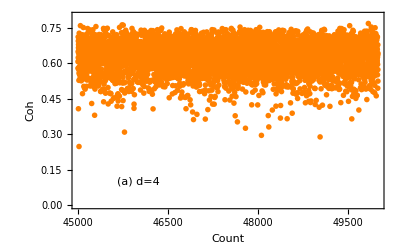

```mathematica
DiscretePlot[T4[i],{i,45000,50000},Filling->None,PlotMarkers->{Automatic,Tiny},Frame->True,PlotRange->{0,0.80},PlotStyle->{Orange},FrameLabel->{"Count","Coh"},LabelStyle->{15,Bold},Epilog->{Text["(a) d=4",{46000,0.1},{0,0}]}]
```

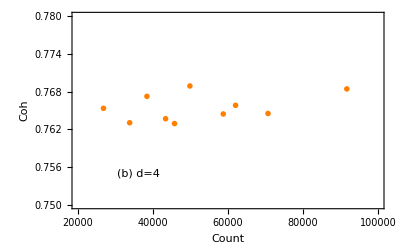

```mathematica
DiscretePlot[T4[i],{i,{45735,33780,43366,58737,70673,26790,62022,38386,91684,49839}},Filling->None,PlotMarkers->{Automatic,Medium},Frame->True,PlotRange->{{20000,100000},{0.75,0.78}},PlotStyle->{Orange},FrameLabel->{"Count","Coh"},LabelStyle->{15,Bold},Epilog->{Text["(b) d=4",{36000,0.755},{0,0}]}]
```

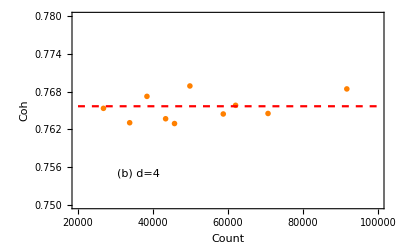

```mathematica
Show[Out[11],ParametricPlot[{x=p,y=0.76568},{p,20000,100000},PlotRange->{{20000,100000},{0.75,0.78}},PlotStyle->{Red,Dashed}]]
```

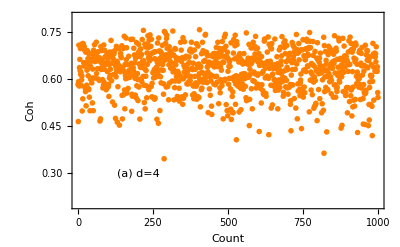

```mathematica
DiscretePlot[T4[i],{i,0,1000},Filling->None,PlotMarkers->{Automatic,Tiny},Frame->True,PlotRange->{0.2,0.80},PlotStyle->{Orange},FrameLabel->{"Count","Coh"},LabelStyle->{15,Bold},Epilog->{Text["(a) d=4",{200,0.3},{0,0}]}]
```

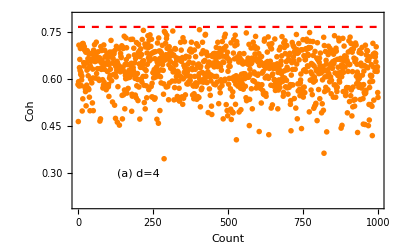

```mathematica
Show[Out[8],ParametricPlot[{x=p,y=0.76568},{p,0,1000},PlotRange->{{0,100000},{0.20,0.78}},PlotStyle->{Red,Dashed}]]
```

```mathematica
Export["fig1.eps",Out[9]]
```

fig1.eps

```mathematica
Export["fig2.eps",Out[13]]
```

fig2.eps

```mathematica
2 √((0.4-0.2)^2+(0.3-0.1)^2)+√((0.4-0.3+0.2-0.1)^2)
```

0.765685

```mathematica
2 √((0.4-0.3)^2+(0.2-0.1)^2)+√((0.4-0.2+0.3-0.1)^2)
```

0.682843

```mathematica
2 √((0.4-0.1)^2+(0.3-0.2)^2)+√((0.4-0.3+0.1-0.2)^2)
```

0.632456

```mathematica
2 √((0.4-0.1)^2+(0.2-0.3)^2)+√((0.4-0.2+0.1-0.3)^2)
```

0.632456

```mathematica
2 √((0.4-0.3)^2+(0.2-0.1)^2)+√((0.4-0.1+0.3-0.2)^2)
```

0.682843

```mathematica
2 √((0.4-0.2)^2+(0.3-0.1)^2)+√((0.4-0.1+0.2-0.3)^2)
```

0.765685

```mathematica
2 √((0.3-0.2)^2+(0.4-0.1)^2)+√((0.3-0.4+0.2-0.1)^2)
```

0.632456

```mathematica
2 √((0.3-0.4)^2+(0.2-0.1)^2)+√((0.3-0.2+0.4-0.1)^2)
```

0.682843

```mathematica
2 √((0.3-0.1)^2+(0.2-0.4)^2)+√((0.3-0.2+0.1-0.4)^2)
```

0.765685

```mathematica
2 √((0.3-0.1)^2+(0.2-0.4)^2)+√((0.3-0.4+0.1-0.2)^2)
```

0.765685

```mathematica
2 √((0.3-0.4)^2+(0.2-0.1)^2)+√((0.3-0.1+0.4-0.2)^2)
```

0.682843

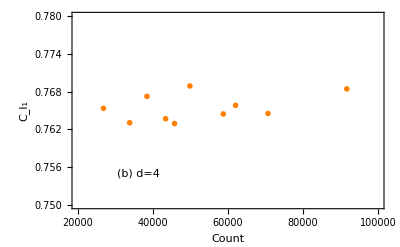

```mathematica
DiscretePlot[T4[i],{i,{45735,33780,43366,58737,70673,26790,62022,38386,91684,49839}},Filling->None,PlotMarkers->{Automatic,Medium},Frame->True,PlotRange->{{20000,100000},{0.75,0.78}},PlotStyle->{Orange},FrameLabel->{"Count","C_l_1"},LabelStyle->{15,Bold},Epilog->{Text["(b) d=4",{36000,0.755},{0,0}]}]
```

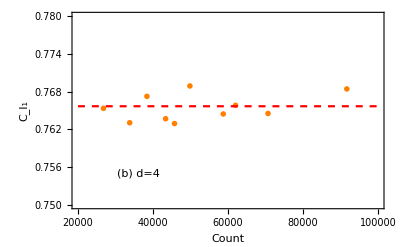

```mathematica
Show[Out[12],ParametricPlot[{x=p,y=0.76568},{p,20000,100000},PlotRange->{{20000,100000},{0.75,0.78}},PlotStyle->{Red,Dashed}]]
```

```mathematica
Export["fig2.eps",Out[13]]
```

fig2.eps

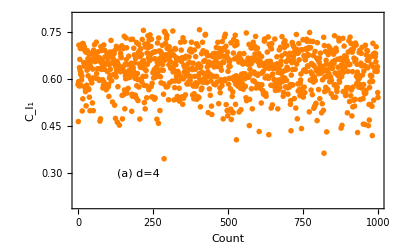

```mathematica
DiscretePlot[T4[i],{i,0,1000},Filling->None,PlotMarkers->{Automatic,Tiny},Frame->True,PlotRange->{0.2,0.80},PlotStyle->{Orange},FrameLabel->{"Count","C_l_1"},LabelStyle->{15,Bold},Epilog->{Text["(a) d=4",{200,0.3},{0,0}]}]
```

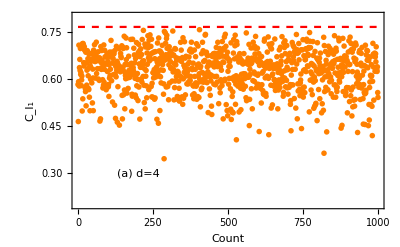

```mathematica
Show[Out[15],ParametricPlot[{x=p,y=0.76568},{p,0,1000},PlotRange->{{0,100000},{0.20,0.78}},PlotStyle->{Red,Dashed}]]
```

```mathematica
Export["fig1.eps",Out[16]]
```

fig1.eps